# 从傅里叶变换到拉普拉斯变换

```mathematica
Manipulate[ParametricPlot[{ReIm@Exp[I ω t]},{t,0,t1},PlotRange->1.2],{{ω,1},0.001,5},{{t1,0.001},0.001,2π}]
```

```mathematica
Manipulate[ParametricPlot[{ReIm@Exp[Complex@@s t],{Cos[t],Sin[t]}Exp[s[[1]]t1]},{t,0,t1},PlotRange->3],{{s,{0.5,0.5}},Locator},{{t1,0.001},0.001,2π}]
```

```mathematica
ComplexPlot3D[z,{z,-3-3I,3+3I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Cos[z],{z,-3-3I,3+3I}]
```

-Graphics3D-

### 对于a x^2

```mathematica
Manipulate[Plot[{a x^2,E^(-b x),a x^2 E^(-b x)},{x,-5,5},PlotLegends->{a x^2,E^(-b x),a x^2 E^(-b x)},PlotRange->{0,100}],{{a,1},0,100},{{b,1},0,10}]
```

### 对于X^x

```mathematica
Manipulate[Plot[{x^x,E^(-b x),x^x E^(-b x)},{x,-5,30},PlotLegends->{x^x,E^(-b x),x^x E^(-b x)},PlotRange->{0,10}],{{b,1},0,10}]
```

### 拉氏变换

```mathematica
LaplaceTransform
```

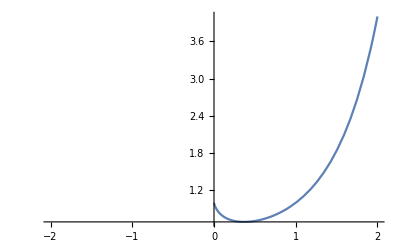

```mathematica
Plot[{x^x},{x,-2,2}]
```

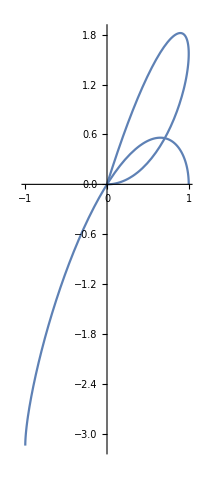

```mathematica
PolarPlot[AbsArg[E^(I ω)],{ω,0,π}]
```

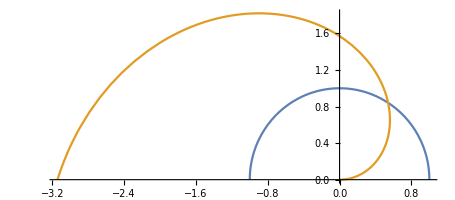

```mathematica
PolarPlot[Evaluate[AbsArg[E^(I ω)]],{ω,0,π}]
```

```mathematica
AbsArg[E^(I ω)]
```

```mathematica
{ⅇ^(-Im[ω]),Arg[ⅇ^(ⅈ ω)]}/.ω->1
```

{1,1}

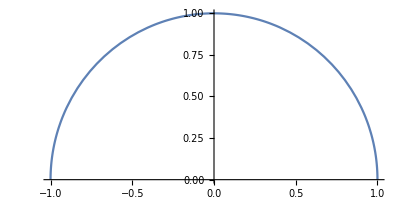

```mathematica
PolarPlot[1,{ω,0,π}]
```

```mathematica
Signal
```